```mathematica
chip[k_Integer?NonNegative,f_]:=chip[k,f]=Block[{x},Integrate[f[x]*ChebyshevT[k,x]/Sqrt[1-x^2],{x,-1,1}]]/Which[k==0,Pi,k>0,Pi/2] (*Generalizes chebyinnerprod to any f *)
chip[5,Sin[ Pi #]&]//N
```

0.104282

```mathematica
Clear[chebyinnerprod,approx]
chebyinnerprod[k_Integer?NonNegative]:=chebyinnerprod[k]=Block[{x},Integrate[(Sin[π x] ChebyshevT[k,x])/Sqrt[1-x^2],{x,-1,1}]]/Which[k==0,π,k>0,π/2] ;
 (*Calculates <Sin(π x ), Tn(x)> where <f,g> is the Chebyshev Inner product, ∫_-1^1 f[x]g[x]*(1-x**2)^(-1/2) ⅆx. f and g need to be scaled from the desired domain to [-1,1]. In this example, Sin is scaled from [-Pi,Pi] to [-1,1], note ef will rescale after we form the polynomial.*)
approx[x_,k_]:=approx[x,k]=Sum[chebyinnerprod[t]*ChebyshevT[t,x],{t,0,k}]
ef[x_,k_]:=approx[x/Pi,k]
```

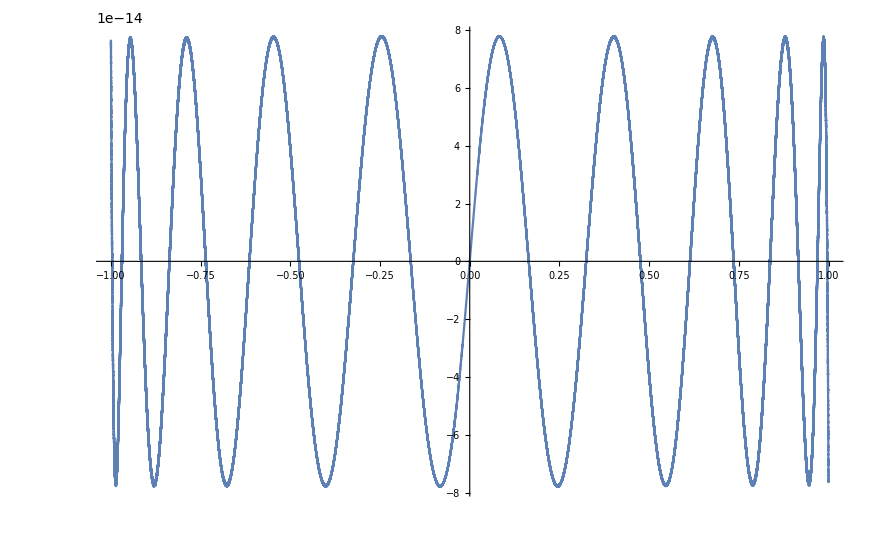

```mathematica
Plot[Evaluate@SetPrecision[Sin[π x]-approx[x,17],32],{x,-1,1},PlotRange->All,PlotPoints->10*^4]
```

```mathematica
$MaxExtraPrecision=100;
table=Table[Sin[x]-ef[x,j],{j,10,40}];
%//TableForm
Table[NMaximize[{table[[j]],-π≤x≤π},x,WorkingPrecision->100],{j,1,Length[table]}]//TableForm
Plot[Evaluate@table[x],{x,-π,π},PlotRange-> All,PlotLegends->Automatic,PlotPoints->250]
```

1
 |  |  |  |

5.942793393861198481453580118347478333335100791982276261400497313423884396065813986790553862436713628×10^-6 | x→0.4455539018495705837986252909757734134158645522006788681995838232613632800386859651485127531649488493
9.621058842076489814976385974735214395903201660569195944354726290641267747929943350828554308712803033×10^-8 | x→-1.111938850586552305229751955611127910948838634699293520297308789037370129582093603511731176440952356
9.621058842076489814976385974735214395903201660569195944354726290641267747929943350828554308712803033×10^-8 | x→-1.111938850586552305229751955611127910948838634699293520297308789037370129582093603511731176440952356
1.156055445062291783394632311834818448462099365494222252625449926788670272020611454507375876221739744×10^-9 | x→0.3279308418752665039106685215572656565366169171081520619567326686943991227273451767342411951492761649
1.156055445062291783394632311834818448462099365494222252625449926788670272020611454507375876221739744×10^-9 | x→0.3279308418752665039106685215572656565366169171081520619567326686943991227273451767342411951492761649
1.065075087648210973563358594405531640313754444202769835827292209460533284174120725860046151457047898×10^-11 | x→0.2895920726685103749319097575189144349178093357702015125876016466338462520393280092163754027786368266
1.065075087648210973563358594405531640313754444202769835827292209460533284174120725860046151457047898×10^-11 | x→0.2895920726685103749319097575189144349178093357702015125876016466338462520393280092163754027786368266
7.739008781836528266137142421781532078697500641637157001304034683386106935558332088420812091002750416×10^-14 | x→2.126946308908853614110782734267668634913789040791559436683993443987835740709796882923949323392568063
7.739008781836528266137142421781532078697500641637157001304034683386106935558332088420812091002750416×10^-14 | x→2.126946308908853614110782734267668634913789040791559436683993443987835740709796882923949323392568063
4.607963336130487968970432973636703358243173342898774872309670001249042000164965890960426868821524196×10^-16 | x→0.2246153173989136127039116736555030272436027716192524127541188844328369605591458899047194014791924628
4.607963336130487968970432973636703358243173342898774872309670001249042000164965890960426868821524196×10^-16 | x→0.2246153173989136127039116736555030272436027716192524127541188844328369605591458899047194014791924628
2.270933577602641875707044223273030205725429554057486648991804938343266894033694530600282498709509892×10^-18 | x→-0.6389352498603971409983445911352215152521268660758040105806487851714335479712482579236027940275780852
2.270933577602641875707044223273030205725429554057486648991804938343266894033694530600282498709509892×10^-18 | x→-0.6389352498603971409983445911352215152521268660758040105806487851714335479712482579236027940275780852
9.375531628226481064422181962414880503307909142637948595632524930556204507287980283317771969151005656×10^-21 | x→2.289794382928065802296983733743377274232925603719031020193714367791232344207655933067645097436021042
9.375531628226481064422181962414880503307909142637948595632524930556204507287980283317771969151005656×10^-21 | x→2.289794382928065802296983733743377274232925603719031020193714367791232344207655933067645097436021042
3.328701330629996600821997104548053322442295631324503138588543069488523793373336011535148870844139643×10^-23 | x→0.1826229987877742964154953060450679007176460893499786270272364508194257235970860684151158119315071906
3.328701330629996600821997104548053322442295631324503138588543069488523793373336011535148870844139643×10^-23 | x→0.1826229987877742964154953060450679007176460893499786270272364508194257235970860684151158119315071906
1.016346474896641336954772128943110968424506363320355423151300648350728467102073042696034253165630754×10^-25 | x→-1.162625745506279020646087803389361343713698873513750273491694506174601887011113092101606957701762187
1.016346474896641336954772128943110968424506363320355423151300648350728467102073042696034253165630754×10^-25 | x→-1.162625745506279020646087803389361343713698873513750273491694506174601887011113092101606957701762187
2.710754328589548096558387184911734151723646706576445589187287140667475102144684006424814955421892324×10^-28 | x→0.7873290067710403813486993832001683242920514520945390415490363615742616266287409845082549392432609621
2.710754328589548096558387184911734151723646706576445589187287140667475102144684006424814955421892324×10^-28 | x→0.7873290067710403813486993832001683242920514520945390415490363615742616266287409845082549392432609621
6.362365450719556584066217044496543553926214303349492902401618972595123079889050895901544385147882469×10^-31 | x→-0.4470365426355560313104932364771587185726520315927467546881668336721976208793759353605634814732323816
6.362365450719556584066217044496543553926214303349492902401618972595123079889050895901544385147882469×10^-31 | x→-0.4470365426355560313104932364771587185726520315927467546881668336721976208793759353605634814732323816
1.319604764018940399755908275254814480278876706903683511329121454349438320807301475947122795434478277×10^-33 | x→-3.091094913535773479384290942906785166796056709705696562297654270612876709714963792057606835281019449
1.319604764018940399755908275254814480278876706903683511329121454349438320807301475947122795434478277×10^-33 | x→-3.091094913535773479384290942906785166796056709705696562297654270612876709714963792057606835281019449
2.46166469140862349277112634364368360111671585553734111534840367875186868394534687767947624322626851×10^-36 | x→0.1333202892095051674275117335947196915713111325275575021191238298640530114362863336946352409145519751
2.46166469140862349277112634364368360111671585553734111534840367875186868394534687767947624322626851×10^-36 | x→0.1333202892095051674275117335947196915713111325275575021191238298640530114362863336946352409145519751
4.09878878273857314676992899483809218647480070295641230112467106629383333069441826486262091381166636×10^-39 | x→-3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068
4.09878878273857314676992899483809218647480070295641230112467106629383333069441826486262091381166636×10^-39 | x→-3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068
6.185719083184021767728609139361068855682988247000792770382790516323067066121529943123020573757913191×10^-42 | x→3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068
6.185719083184021767728609139361068855682988247000792770382790516323067066121529943123020573757913191×10^-42 | x→3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

-Graphics-